# Homework 11

## Problem 11.1

A small mass m slides in a frictionless bowl that has a height given by the function z(x,y) = (1/10) x^2+c y^2 where all the constants are in SI units. Assume that the z component of velocity is small enough that it can be ignored.

```mathematica
Clear["`*"]
```

## Part A

First, write down U as a function of x[t] and y[t], and take the gradient of it to find the force. Use the function notation x[t] and y[t] so that we can use these for solving the differential equations later.

```mathematica
U=m*g*((1/10)*(x[t])^2+c*(y[t])^2)
F= -Grad[U,{x[t],y[t],z[t]},"Cartesian"]
```

g m (x[t]^2/10+c y[t]^2)

{-1/5 g m x[t],-2 c g m y[t],0}

```mathematica
F[[1]]
```

-1/5 g m x[t]

Now, solve the differential equations from Newton’s 2nd Law in x and y to find the frequency. You need not include initial conditions.

```mathematica
DSolve[F[[1]]==x''[t]*m,x[t],t][[1,1]]
DSolve[F[[2]]==y''[t]*m,y[t],t][[1,1]]
```

x[t]→C[1] Cos[(√g t)/(√5)]+C[2] Sin[(√g t)/(√5)]

y[t]→C[1] Cos[√2 √c √g t]+C[2] Sin[√2 √c √g t]

Once you have solved each equation, you can read ω from the argument of the sine and cosine functions. Use this to fill in wx and wy in cell below. If you see any strange terms like e^(0*t√g), ignore them. Mathematica does not know that t and g are not infinity.

Finally, we can find the value of c that gives a frequency 3 times larger in the y equation than in the x equation.

```mathematica
wx=Sqrt[g]/Sqrt[5];
wy=Sqrt[2]*Sqrt[c]*Sqrt[g];
Solve[wy/wx==3,c][[1,1]]
```

c→9/10

```mathematica
c=9/10
```

9/10

### Solution

```mathematica
If[Abs[c-.9]<=.001,Print["C is correct"],Print["C is not correct"]]
```

C is correct

## Part B

Now we’ll plot the motion for initial conditions x(0)=0.2 m, y(0)=0, vx(0)=0, vy(0)=0.5 m/s. Use g=9.8 m/s^2 and m=0.015 kg.

```mathematica
g=9.8;
m=.015;
x=x[t]/.DSolve[{F[[1]]==x''[t]*m,x[0]==0.2,x'[0]==0},x[t],t][[1]]
y=y[t]/.DSolve[{F[[2]]==y''[t]*m,y[0]==0,y'[0]==0.5},y[t],t][[1]]
```

0.2 Cos[1.4 t]

0.119048 Sin[4.2 t]

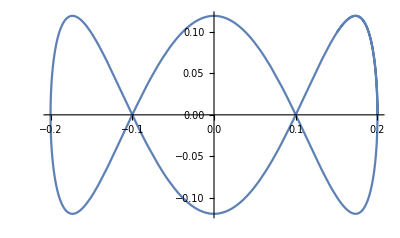

```mathematica
ParametricPlot[{x,y},{t,0,5}]
```

## Problem 11.2

Solve the damped HO equation with differing values of the damping constant and various initial conditions. Make plots for underdamped, overdamped, and critically damped cases. Be sure to run Clear[“`*”] between various sets of parameters and initial conditions.

```mathematica
Clear["`*"]
```

Underdamped

(ⅇ^-t Sin[2 √2 t])/(2 √2)

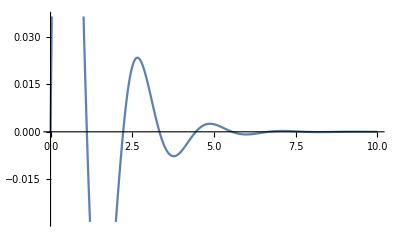

```mathematica
eq1=x''[t]+2beta x'[t]+w0^2 x[t]==0;

x=x[t]/.DSolve[{eq1/.{beta->1,w0->3},x[0]==0,x'[0]==1},x[t],t][[1]]
Plot[x,{t,0,10}]
```

```mathematica
Clear["`*"]
```

Overdamped

0.57735 ⅇ^(-2. t) (-1. ⅇ^(0.133975 t)+1. ⅇ^(1.86603 t))

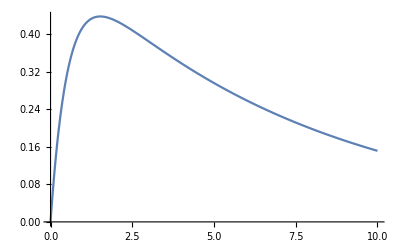

```mathematica
eq1=x''[t]+2beta x'[t]+w0^2 x[t]==0;

x=x[t]/.DSolve[{eq1/.{beta->1,w0->0.5},x[0]==0,x'[0]==1},x[t],t][[1]]
Plot[x,{t,0,10}]
```

```mathematica
Clear["`*"]
```

Critically damped

ⅇ^-t t

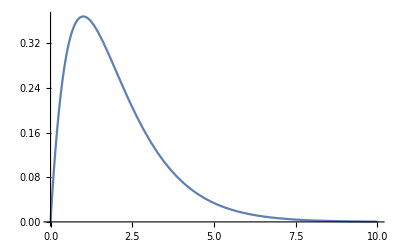

```mathematica
eq1=x''[t]+2beta x'[t]+w0^2 x[t]==0;

x=x[t]/.DSolve[{eq1/.{beta->1,w0->1},x[0]==0,x'[0]==1},x[t],t][[1]]
Plot[x,{t,0,10}]
```

## Problem 11.3

A massless spring of spring constant k=3.24 N/m is hung from the ceiling. We call the bottom end of the spring y=0. A mass of 125 g is hung from the spring. It takes 24.0 sec for the amplitude of the spring’s oscillations to reduce to 1/2 of their initial value. What is the value of the damping constant ? What is the value of omega0? What is the oscillation frequency omega1?

```mathematica
Clear["`*"]
```

```mathematica
k=3.24
m=.125
beta=beta/.Solve[1/2==E^(-beta*24)][[1]]
omega0=Sqrt[k/m]
omega1=Sqrt[omega0^2+beta^2]//N
```

3.24

0.125

0.+4. b

5.09117

√(25.92+(0.+4. b)^2)

### Solutions

```mathematica
If[Simplify[Abs[beta-.0288811]/beta]<.01,Print["beta is correct"],Print["beta is incorrect"]]
If[Simplify[Abs[omega0-5.091168825]]<.01,Print["omega0 is correct"],Print["omega0 is incorrect"]]
If[Simplify[Abs[omega1-5.091086906]]<.01,Print["omega1 is correct"],Print["omega1 is not correct"]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of beta/.????.

Hold[If[Simplify[Abs[beta-0.0288811]/beta]<0.01,Print[beta is correct],Print[beta is incorrect]]]

omega0 is correct

omega1 is correct

## Written Problems

-Graphics-